```mathematica
g=0.2573
```

0.2573

```mathematica
w[r_]:=2.94 Sin[1.24 Sin[0.47 r+1.94]-9.55]+3.53
```

```mathematica
w[0]
```

1.0077

```mathematica
H[r_]:=w[r]/r^2 √(1+(w[r0]^2/r0^4)/(w[r]^2/r^4-w[r0]^2/r0^4))
taylorSeries=Series[H[r],{r,0,1}];
w[0]/r^2+w'[0]/r+w''[0]/2

Ea[r0_]:=2g NIntegrate[w[r]/r^2 √(1+(w[r0]^2/r0^4)/(w[r]^2/r^4-w[r0]^2/r0^4))-w[0]/r^2-w'[0]/r,{r,0,r0}]-(2g)/r0*w[0]+2*g*w'[0]*Log[r0]
```

0.189715+0.991003/r^2+0.375109/r

ListLinePlot::lpn: datat2 不是由数字或者数对组成的列表.

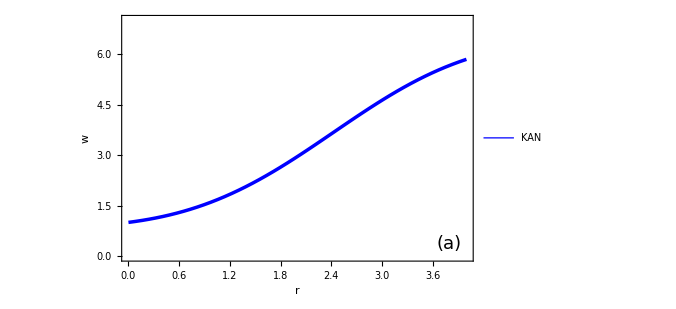

```mathematica
Plot[w[r],{r,0,4},PlotRange->{{0,4},{0.00001,7}},Frame->True,FrameLabel->{Style["r",FontFamily->"Times New Roman",FontSlant->Italic],Style["w",FontFamily->"Times New Roman",FontSlant->Italic]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ImageSize->{500,300},PlotStyle->{Blue,Thickness[0.005]},PlotLegends->Placed[LineLegend[{Directive[Blue,Thickness[0.005]]},{Style["KAN",FontSize->15,Black]},LegendMarkerSize->40],{0.2,0.9}],Epilog->{Text[Style["(a)",FontSize->18,FontFamily->"Times New Roman"],{3.8,0.1},{Center,Bottom}]},(*手动覆盖显示横坐标的 "0.0"*)Epilog->{Text[Style["0.0",14,FontFamily->"Times New Roman"],{0,0},{1.5,-1.5},(*调整文本位置，对齐横坐标*)Background->White       (*用白色背景覆盖默认标签*)]}]
```

```mathematica
Laa[r0_]:=2*0.1973NIntegrate[√((w[r0]^2/r0^4)/(w[r]^2/r^4-w[r0]^2/r0^4)),{r,0,r0}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

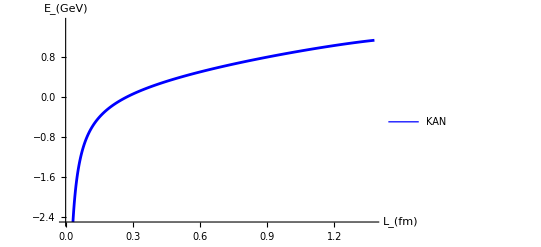

```mathematica
fig=ListLinePlot[ParallelTable[{Re[Laa[r0]],Re[Ea[r0]]},{r0,0,4,0.01}],AxesLabel->{Style["\!\(\*SubscriptBox[\(L\), \(\\\ \)]\)(fm)",20,Black],Style["\!\(\*SubscriptBox[\(E\), \(\\\ \)]\)(GeV)",20,Black]},AxesStyle->Directive[Black,20],BaseStyle->{Thick},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],PlotStyle->{Directive[Blue,Thickness[0.005]]},AxesOrigin->{0,-2.5},PlotRange->{{0,1.37},{-2.5,1.5}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thickness[0.005]]},{Style["KAN",FontSize->15,Black]},(*设置字体大小*)LegendMarkerSize->40],{0.2,0.9}  (*图例位置*)]]
```

```mathematica
H[L_]:=0.8404*L-0.0866/L+0.1033
```

```mathematica
H[0.4357]
```

0.270702

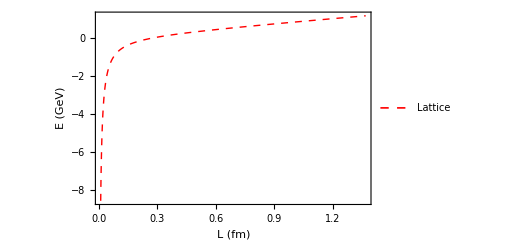

```mathematica
(*绘制图形*)fig0=Plot[H[L],{L,0.01,1.37},PlotRange->All,AxesLabel->{"L (fm)","E (GeV)"},Frame->True,FrameLabel->{"L (fm)","E (GeV)"},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],LabelStyle->Directive[Black,16],(*保持默认字体*)PlotStyle->{Directive[Dashed,Red,Thickness[0.005]],Thick},(*设置为红色虚线*)PlotLegends->Placed[LineLegend[{Directive[Dashed,Red,Thickness[0.005]]},{"Lattice"},LegendMarkerSize->30],{0.2,0.9}]  (*添加图例*)]
```

```mathematica
Show[{fig,fig0},Frame->True,FrameStyle->Directive[Black,Thin,FontFamily->"Times New Roman"],FrameLabel->{DisplayForm[RowBox[{"L"}]],DisplayForm[RowBox[{"E"}]]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ImageSize->{500,300},Epilog->{Text[Style["(b)",FontSize->16,FontFamily->"Times New Roman"],{1.3,-2.4},{Center,Bottom}]}]
```

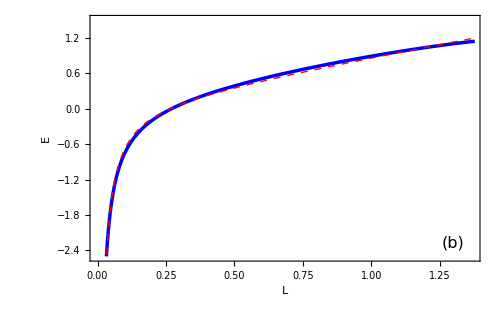

NIntegrate::write: #2 中的标签 Slot 被保护.

General::stop: 在本次计算中，NIntegrate::nlim 的进一步输出将被抑制.

NIntegrate::nlim: r = r0 不是积分的一个有效的极限.

N::nosym: N[r_] 不包含附加规则的符号.

NIntegrate::nlim: r = r0 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate::nlim 的进一步输出将被抑制.

NIntegrate::write: #2 中的标签 Slot 被保护.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.